## Глава 3 Операционное исчисление в СКМ Mathematica

## §1. Преобразование Лапласа

### 1.1. Определение и свойства преобразования Лапласа.

Преобразованием Лапласа функции f(t), t∈ℝ (которая, может принимать и комплексные значения), называется функция F(p) комплексной переменной p, определяемая следующим равенством:

F(p)=∫_0^(+∞) e^(-p t)f(t)ⅆt

Оригиналом называется всякая функция f(t), удовлетворяющая следующим условиям:

1) f(t)=0 при t<0, причем принимается, что f(0)=f(+0);

2) Существуют такие постоянные σ и M, что:

|f(t)|<M ⅇ^(σ t) при t>0

(величина σ_0=inf σ называется показателем роста функции f(t));

3) На любом конечном отрезке [0;T] функция может иметь лишь конечное число точек разрыва, причем только 1-ого рода.

Если f(t) - оригинал, то стоящий в правой части равенства (1) интеграл Лапласа сходится абсолютно и равномерно в полуплоскости Re p  ⩾ σ>σ_0. При этом функция F(p) является аналитической в полуплоскости Re p> σ_0 и называется изображением функции f(t).

Соответствие между оригиналом f(t) и его изображением F(p) символически записывается в виде f(t)≐F(p)

##### Пример №13.10

Рассмотрим простейший пример: Используя формулу (1), найти изображение для следующего оригинала:

f(t)=Piecewise[{{t, 0≤ t<2}, {1/2(4-t), 2≤ t<4}, {0, 4≤ t}}]

Запишем исходную кусочно-заданную функцию:

```mathematica
f[t_]:=Piecewise[{{t,0≤ t<2},{1/2(4-t),2≤ t<4}},0]
```

Для наглядности построим ее график :

```mathematica
Plot[f[t],{t,-2,6}]
```

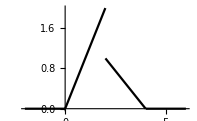

Очевидно, что данная функция является оригиналом, т.к. соблюдены все условия изложенные выше.

Для того чтобы найти изображение, воспользуемся формулой (1). Обозначать изображения будем fp(p), т.к. функции начинающиеся с большой буквы, в основном, являются системными, т.е. встроенными.

```mathematica
fp[p_]:=Integrate[Exp[-p t]f[t],{t,0,Infinity}]
```

```mathematica
fp[p_]:=Integrate[Exp[-k t]f[t],{t,0,Infinity}]/.k-> p
```

Существует принципиальное отличие, между двумя выражениями, записанными выше. Первое интерпретируется следующим образом: каждый раз при вызове функции fp(p_1) в переменную p, стоящую внутри интеграла, передается значение p_1 и затем вычисляется весь интеграл. Можно догадаться, что это замедляет работу программы, поэтому используется второй способ: сначала вычисляется интеграл, зависящий от k, затем переменная k просто заменяется на значение p_1. Данный способ работает быстрее, т.к. интеграл не будет вычисляться столько раз, сколько мы вызвали функцию fp(p) .

Выведем полученную функцию:

```mathematica
fp[p]
```

(ⅇ^(-4 p) (1-3 ⅇ^(2 p)+2 ⅇ^(4 p)-2 ⅇ^(2 p) p))/(2 p^2)

Ответ:

f(t)≐(ⅇ^(-4 p) (1-3 ⅇ^(2 p)+2 ⅇ^(4 p)-2 ⅇ^(2 p) p))/(2 p^2)

##### Пример №1

Найти изображение функции Хевисайда:

H(t)=η(t)=Piecewise[{{1, t≥ 0}, {0, t<0}}]

Функция Хевисайда в Mathematica является встроенной. Конечно, можно определить ее самостоятельно при помощи кусочно-заданной функции PieceWise, но в этом нет необходимости. Функция PieceWise записывается следующим образом:

```mathematica
h[t_]:=HeavisideTheta[t]
Plot[h[t],{t,-2,2}]
```

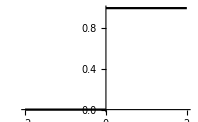

Так как функция Хевисайда является оригиналом, то ее изображение:

```mathematica
hp[p_]:=Integrate[Exp[-k t]h[t],{t,0,Infinity}]/.k-> p
```

```mathematica
Simplify[hp[p],Re[p]>0]
```

1/p

Получили H(t)≐p^-1.

### 1.2 Свойства преобразования Лапласа.

1. С в о й с т в о  л и н е й н о с т и.

∑_(k=1)^n C_k f_k(t)≐∑_(k=1)^n C_k F_k(p),  Re p> max{σ_1,σ_2,... σ_n}

2. Т е о р е м а  п о д о б и я.

f(t/α)≐1/α F(p/α), Re p>α σ_0

3. Т е о р е м а  с м е щ е н и я. Умножению оригинала на ⅇ^(α t),α∈ℝ, соответствует смещение аргумента изображения на α, т.е.:

ⅇ^(α t)f(t)≐F(p-α), Re(p-α)>σ_0

4. Т е о р е м а   з а п а з д ы в а н и я. Запаздыванию оригинала на τ соответствует умножение изображения на ⅇ^(-p τ):

η(t-τ)f(t)≐ⅇ^(-p τ)F(p), Re p > σ_0

5. Д и ф ф е р е н ц и р о в а н и е  о р и г и н а л а.  Если f(t) и ее производные f^(k)(t) являются оригиналами, то для любого k=1,2...n

f^(k)(t)≐p^k F(p)-(p^(k-1)f(0)+p^(k-2)f'(0)+...+f^(k-1)(0))

В частности,

f'(t)≐p F(p)-f(0), Re p> σ_0

6. И н т е г р и р о в а н и е  о р и г и н а л а:

∫_0^t f(τ)ⅆτ≐(F(p))/p, Re p> σ_0

7. Д и ф ф е р е н ц и р о в а н и е  и з о б р а ж е н и я. Умножению оригинала на множитель t соответствует умножению изображения на -1 и дифференцирование его по аргументу  p:

(t
□)^n f(t)≐(-1)^n F^(n)(p), n=1,2...

8. И н те г р и р о в а н и е  и з о б р а ж е н и я. Если f(t)/t является оригиналом, то

1/t f(t)≐∫_p^(+∞) F(q)ⅆq

9. Д и ф ф е р е н ц и р о в а н и е  и  и н т е г р и р о в а н и е  п о  п а р а м е т р у. Если f(t,α)≐F(p,α) и функции ∂/(∂α)f(t,α) и ∫_α1^α2 f(t,α)ⅆα, рассматриваемые как функции переменной t, являются оригиналами, то

∂/(∂α)f(t,α)≐∂/(∂α)F(p,α)      и      ∫_α1^α2 f(t,α)ⅆα=∫_α1^α2 F(p,α)ⅆα

10. Т е о р е м а  Б о р е л я  о б  и з о б р а ж е н и и  с в е р т к и. Свертке оригиналов

f_1*f_2=∫_0^t f_1(τ)f_2(t-τ)ⅆτ=∫_0^t f_1(t-τ)f_2(τ)ⅆτ

соответствует произведение изображений, т. е.

f_1*f_2=F_1(p)·F_2(p)

11. И н т е г р а л  Д ю а м е л я. Если f(t)≐F(p) и g(t)≐G(p), то

p F(p) G(p)≐f(o)g(t)+(f'*g)(t)=g(0)f(t)+(g'*f)(t)

Ниже приведен список изображений наиболее распространенных функций:

η(t)≐1/p                                                      t^n≐(n!)/p^(n+1)
ch β t≐p/(p^2-β^2)                          sh β t≐β/(p^2-β^2)
ⅇ^(α t)≐1/(p-α)                           t^n ⅇ^(α t)≐(n!)/(p-α)^(n+1)
cos β t ≐p/(p^2+β^2)                      sin β t≐β/(p^2+β^2)

С помощью свойств преобразования Лапласа и списка основных изображений можно найти изображения большинства функций встречающихся на практике.

Рассмотрим пример:

##### Пример №13.19

Найти изображение заданной функции:

f(t)=e^-t+3 e^(-2t)+t^2

Согласно свойству линейности изображение суммы функций равно сумме изображений. Используя список изображений (3), находим :

e^-t=1/(p+1)
3 e^(-2t)=3/(p+2)
t^2=2/p^3

В итоге, изображение исходной функции:

f(t)≐F(p)
F(p)=1/(p+1)+3/(p+2)+2/p^3

##### Пример №13.22

Найти изображение заданной функции:

f(t)=sin^2(t-a)

Применяя тригонометрические тождества, приведем функцию к виду:

sin^2(t-a)=1/2(1-cos(2(t-a)))
cos(2(t-a))=cos 2t cos 2a + sin 2t sin 2a
sin^2(t-a)=1/2(1-cos 2t cos 2a - sin 2t sin 2a)

Воспользуемся свойством линейности и списком изображений:

cos 2t≐p/(p^2+4),  sin 2t≐2/(p^2+4)

Получаем изображение исходной функции:

F(p)=1/2(1/p-(p cos 2a)/(p^2+4)-(2sin 2a)/(p^2+4))

##### Пример №13.32

Найти изображение заданной функции:

f(t)=ⅇ^-t sin^2(t)

Чтобы найти изображение, воспользуемся выражением, полученным в предыдущем примере. Так как a=0, то:

(sin(t))^2≐1/2(1/p-p/(p^2+4))

Теперь согласно теореме смещения получаем ответ:

ⅇ^-t sin^2(t)≐1/2(1/(p+1)-p/((p+1)^2+4))

##### Пример №13.36

Найти изображение заданной функции:

f(t)=∫_0^t ⅇ^(-1/2(t-τ))τⅆτ

Заданная функция представляет из себя свертку двух функций:

ⅇ^(-1/2t)*t=∫_0^t ⅇ^(-1/2(t-τ))τⅆτ=∫_0^t ⅇ^(-1/2τ)(t-τ)ⅆτ

По теореме Бореля об изображении свертки получаем изображение:

ⅇ^(-1/2t)*t≐1/p^2 1/(p+1/2)=2/(p^2(2p+1))

##### Пример №13.44

Найти изображение дифференциального выражения при заданных начальных условиях:

x^IV(t)+4x'''(t)+2x''(t)-3x'(t)-5,  x(0)=x'(0)=x''(0)=x'''(0)=0

Обозначим изображение функции x(t) как X(p), тогда согласно свойству дифференцирования оригинала получаем:

x^IV(t)≐p^4 X(p)-(p^3 f(0)+p^2 f'(0)+p f''(0)+f'''(0)=p^4 X(p)

Так как начальные условия нулевые, получим следующее изображение исходного выражения:

X(p)(p^4+4 p^3+2 p^2-3p)-5/p

Все рассмотренные выше примеры мало относятся к теме данной книги (компьютерные технологии). Они были решены традиционными методами: в каждой задаче приходилось выбирать нужные свойства и каждый раз смотреть в таблицу изображений. Разумеется, процесс решения данного класса задач может быть существенно упрощен с использованием внутренних функций Mathematica. Рассмотрим простейший пример.

##### Пример №13.27

Найти изображение заданной функции:

f(t)=sin t- t cos t

В обычном случае нам было бы необходимо воспользоваться рядом свойств (линейности и дифференцирования изображения), чтобы с помощью изображений известных простейших функций получить изображение заданной.

Функция LaplaceTransform заменяет все эти действия. Рассмотрим пример работы:

```mathematica
LaplaceTransform[Cos[t],t,p]
```

p/(1+p^2)

```mathematica
LaplaceTransform[t Cos[t],t,p]
```

(-1+p^2)/((1+p^2)^2)

Данная функция сама подбирает нужные свойства и находит изображение.

Изображение заданной функции:

```mathematica
LaplaceTransform[Sin[t]-Cos[t]t,t,p]
```

-(-1+p^2)/((1+p^2)^2)+1/(1+p^2)

Рассмотрим ряд примеров:

##### Пример №13.25

f(t)=sh (3t) cos (2t)

```mathematica
LaplaceTransform[Sinh[3t]Cos[2t],t,p]
```

-(3 (13-p^2))/((13-6 p+p^2) (13+6 p+p^2))

F(p)=-(3 (13-p^2))/((13-6 p+p^2) (13+6 p+p^2))

##### Пример №13.37

f(t)=∫_0^t (t-τ)^2 cos 2τⅆτ

```mathematica
LaplaceTransform[Integrate[(t-τ)^2 Cos[2τ],{τ,0,t}],t,p]//Simplify
```

2/(4 p^2+p^4)

F(p)=2/(4 p^2+p^4)

##### Пример №13.42

f(t)=∫_0^t (cos β τ-cos α τ)/τ ⅆτ

```mathematica
LaplaceTransform[Integrate[(Cos[β τ]-Cos[α τ])/τ,{τ,0,t}],t,p]
```

Log[1+p^2/α^2]/(2 p)+Log[α]/p-Log[1+p^2/β^2]/(2 p)-Log[β]/p

F(p)=1/(2p)ln((α^2+p^2)/(β^2+p^2))

Также с использованием данной функции становится удобно находить изображения дифференциальных выражений:

##### Пример №13.42

Найти изображение дифференциального выражения при заданных начальных условиях:

x'''(t)+6x''(t)+x'(t)-2x(t),     x(0)=x'(0)=0,   x''(0)=1

Применим функцию LaplaceTransofrm непосредственно ко всему выражению:

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]
```

-2 LaplaceTransform[x[t],t,p]+p LaplaceTransform[x[t],t,p]+p^3 LaplaceTransform[x[t],t,p]-x[0]-p^2 x[0]+6 (p^2 LaplaceTransform[x[t],t,p]-p x[0]-x'[0])-p x'[0]-x''[0]

Обратим внимание на LaplaceTransorm[x[t],t,p]. Данная функция, зависящая от p, есть ни что иное, как изображение функции x(t). Заменим его на X(p):

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]/.LaplaceTransform[x[t],t,p]-> X[p]
```

-x[0]-p^2 x[0]-2 X[p]+p X[p]+p^3 X[p]+6 (-p x[0]+p^2 X[p]-x'[0])-p x'[0]-x''[0]

Теперь тем же способом можно учесть начальные условия:

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]/.{LaplaceTransform[x[t],t,p]-> X[p],x[0]-> 0,x'[0]-> 0,x''[0]-> 1}
```

-1-2 X[p]+p X[p]+6 p^2 X[p]+p^3 X[p]

В итоге, получили:

-1+X(p)(-2 +p+6 p^2+p^3 )

##### Модуль

Составим программный модуль, который будет находить изображения дифференциальных выражений с учетом начальных условий (или без них):

```mathematica
laplaceD[t_,expr_,rule_]:=Module[{},
Collect[LaplaceTransform[expr,t,p]/.LaplaceTransform[x[t],t,p]-> X[p]/.rule,X[p]]]
```

Пример работы:

##### Пример №13.46

Найти изображение дифференциального выражения при заданных начальных условиях:

x''(t)+5x'(t)-7x(t)+2,     x(0)=α, x'(0)=0

```mathematica
laplaceD[t,x''[t]+5x'[t]-7x[t]+2,{x[0]-> α,x'[0]-> 0}]
```

2/p-5 α-p α+(-7+5 p+p^2) X[p]

##### Пример №13.113

Найти изображение дифференциального выражения при заданных начальных условиях:

x''(t)-2x'(t)+2x=sin t, x(0)=0,  x'(0)=1

```mathematica
laplaceD[t,x''[t]-2x'[t]+2x[t]==Sin[t],{x[0]-> 0,x'[0]-> 1}]
```

-1+(2-2 p+p^2) X[p]==1/(1+p^2)

##### Пример №13.53

Найти изображение следующей функции:

f(t)=Piecewise[{{h/τ t, 0≤ t<τ}, {h, τ≤t≤ 2τ}, {-h/τ(t-3τ), 2τ≤ t<3τ}, {0, t≥ 3τ}}]

Данный пример не представляет абсолютно никакой сложности,  поэтому решим его при помощи функции LaplaceTransform.

Запишем функцию:

```mathematica
f[t_]:=Piecewise[{{h/τ t,0≤ t<τ},{h,τ≤ t< 2τ},{-h/τ(t-3τ),2τ≤ t<3τ}}]
```

Построим ее график, при h=1,τ=π:

```mathematica
Plot[f[t]/.{h-> 1,τ-> Pi},{t,-1Pi,4Pi}]
```

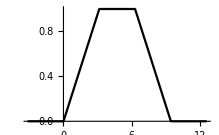

Теперь найдем изображение:

```mathematica
Simplify[LaplaceTransform[f[t],t,p],τ>0]
```

(ⅇ^(-3 p τ) (-1+ⅇ^(p τ))^2 (1+ⅇ^(p τ)) h)/(p^2 τ)

На данном этапе оставим тему поиска изображений.